```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210421_OR_model_and_other_lines_sliding"];
```

FBA Model Network

```mathematica
stoichioforhomosapiens=Drop[Import["../210324_disc_time_windows_and_OR_model/iAT_PLT_636_stoichiomat.csv",HeaderLines->1],None,{1}];
SparseArray@stoichioforhomosapiens
```

SparseArray[…]

```mathematica
stochmatrix=stoichioforhomosapiens;
AdjmatR=Transpose[stochmatrix].stochmatrix;
NormAdjmatR=AdjmatR/.x_/;x≠0->1;
NormAdjmatR=NormAdjmatR/. 0.->0;
NormAdjmatR=UpperTriangularize[NormAdjmatR,1]+LowerTriangularize[NormAdjmatR,-1];
AdjmatM=stochmatrix.Transpose[stochmatrix];
NormAdjmatM=AdjmatM/.x_/;x≠0->1;
NormAdjmatM=NormAdjmatM/. 0.->0;
NormAdjmatM=UpperTriangularize[NormAdjmatM,1]+LowerTriangularize[NormAdjmatM,-1];
```

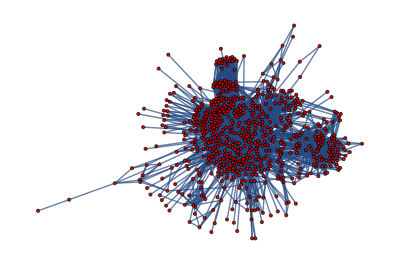

```mathematica
(*AdjacencyGraph[NormAdjmatR,{DirectedEdges->False,VertexSize->6,VertexStyle->Red(*,VertexLabels->{1->"v1",2->"v2",3->"v3",4->"v4",5->"b1",6->"b2",7->"b3"}*)}]*)AdjacencyGraph[NormAdjmatM,{DirectedEdges->False,VertexSize->6,VertexStyle->Red(*,VertexLabels->{1->"A",2->"B",3->"C"}*)}]
```

```mathematica
stoichiometricmatrix=stoichioforhomosapiens;
metabolites=738;
fluxexchanges=1008;
steadystatevector=ConstantArray[{0,0},metabolites];
boundaries=ConstantArray[{0,500},fluxexchanges];
first[a_]:=First/@GatherBy[Ordering@a,a[[#]]&]//Sort;
```

```mathematica
syntheticseqgenerator[stoichiometricmatrix_,steadystatevector_,boundaries_,fluxexchanges_,sequencesize_]:=Module[{subsetsizechoice,subsetpositions,coefficients,objectivefunctions,solutionvectors},
subsetsizechoice=RandomInteger[{1,fluxexchanges}];
subsetpositions=RandomSample[Range@fluxexchanges,subsetsizechoice];
coefficients=Table[RandomReal[{-2,2},subsetsizechoice],sequencesize];
objectivefunctions=Table[ReplacePart[ConstantArray[0.,fluxexchanges],MapThread[#1->#2&,{subsetpositions,coefficients[[i]]}]],{i,sequencesize}];
solutionvectors=Table[LinearProgramming[-objectivefunctions[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@objectivefunctions}]]
```

```mathematica
SeedRandom@5;
AbsoluteTiming[sequences=Table[syntheticseqgenerator[stoichiometricmatrix,steadystatevector,boundaries,fluxexchanges,300],200];]
sequenceschopped=Chop[sequences,10^-5];
```

```mathematica
Table[Length@((sequenceschopped[[i]])[[first@sequenceschopped[[i]],All]]),{i,200}]
Length@(Flatten[sequenceschopped,1])[[first@Flatten[sequenceschopped,1],All]]
Dimensions@(Flatten[sequenceschopped,1])[[All,first[(Flatten[sequenceschopped,1])ᵀ]]]
```

Varying Amount of Selected Subsets

```mathematica
syntheticseqgeneratorfxdsubsetsize[stoichiometricmatrix_,steadystatevector_,boundaries_,fluxexchanges_,sequencesize_,subsetnumber_]:=Module[{subsetsizechoice,subsetpositions,coefficients,objectivefunctions,solutionvectors},
subsetsizechoice=subsetnumber;
subsetpositions=RandomSample[Range@fluxexchanges,subsetsizechoice];
coefficients=Table[RandomReal[{-2,2},subsetsizechoice],sequencesize];
objectivefunctions=Table[ReplacePart[ConstantArray[0.,fluxexchanges],MapThread[#1->#2&,{subsetpositions,coefficients[[i]]}]],{i,sequencesize}];
solutionvectors=Table[LinearProgramming[-objectivefunctions[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@objectivefunctions}]]
```

```mathematica
subsetamounts=Range[100,1000,100];
SeedRandom@5;
AbsoluteTiming[sequencesfixedsubsetsize=Table[Table[syntheticseqgeneratorfxdsubsetsize[stoichiometricmatrix,steadystatevector,boundaries,fluxexchanges,10,i],10],{i,subsetamounts}];]
sequenceschopped=Table[Chop[i,10^-5],{i,sequencesfixedsubsetsize}];
uniquefluxexchanges=Table[Length@first[(Flatten[i,1])ᵀ],{i,sequenceschopped}];
uniqueevents=Table[Length@(Flatten[i,1])[[first@Flatten[i,1],All]],{i,sequenceschopped}];
```

{30.5997,Null}

```mathematica
Thread[{subsetamounts,uniqueevents}]
```

{{100,89},{200,81},{300,82},{400,54},{500,73},{600,53},{700,58},{800,57},{900,47},{1000,48}}

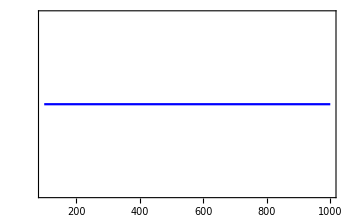
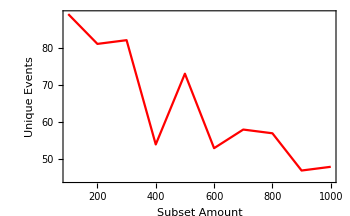

```mathematica
plot1=Overlay[{ListLinePlot[Thread[{subsetamounts,uniquefluxexchanges}],Frame->True,ImagePadding->35,FrameTicks->{{None,All},{All,None}},FrameLabel->{{None,Style["Unique Flux Exchanges",Blue]},{None,None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{First@subsetamounts,Last@subsetamounts},All}],ListLinePlot[Thread[{subsetamounts,uniqueevents}],Frame->True,ImagePadding->35,FrameTicks->{{All,None},{All,None}},FrameLabel->{"Subset Amount",Style["Unique Events",Red]},PlotStyle->Red,ImageSize->350,PlotRange->{{First@subsetamounts,Last@subsetamounts},All}]}]
```

Varying Range of Objective Function Coefficients

```mathematica
boundaries=ConstantArray[{0,500},fluxexchanges];
coefboundaries={{0,1},{-1,0},{0,2},{-2,0},{-1,1},{-2,2},{-3,3},{0,5},{0,-5},{1,1},{-5,5},{-4,4}};
```

```mathematica
syntheticseqgeneratorfxdsubsetsizevaryingcoeff[stoichiometricmatrix_,steadystatevector_,boundaries_,fluxexchanges_,sequencesize_,subsetnumber_,coefboundaries_]:=Module[{subsetsizechoice,subsetpositions,coefficients,objectivefunctions,solutionvectors},
subsetsizechoice=subsetnumber;
subsetpositions=RandomSample[Range@fluxexchanges,subsetsizechoice];
coefficients=Table[RandomReal[coefboundaries,subsetsizechoice],sequencesize];
objectivefunctions=Table[ReplacePart[ConstantArray[0.,fluxexchanges],MapThread[#1->#2&,{subsetpositions,coefficients[[i]]}]],{i,sequencesize}];
solutionvectors=Table[LinearProgramming[-objectivefunctions[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@objectivefunctions}]]
```

```mathematica
SeedRandom@5;
AbsoluteTiming[sequencesfixedsubsetsize=Table[Table[syntheticseqgeneratorfxdsubsetsizevaryingcoeff[stoichiometricmatrix,steadystatevector,boundaries,fluxexchanges,10,20,i],10],{i,coefboundaries}];]
sequenceschopped=Table[Chop[i,10^-5],{i,sequencesfixedsubsetsize}];
uniquefluxexchanges=Table[Length@first[(Flatten[i,1])ᵀ],{i,sequenceschopped}];
uniqueevents=Table[Length@(Flatten[i,1])[[first@Flatten[i,1],All]],{i,sequenceschopped}];
```

{32.9353,Null}

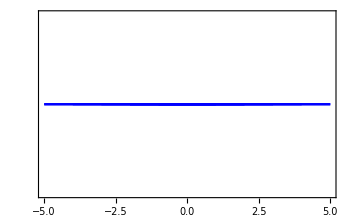
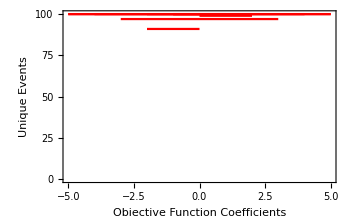

```mathematica
plot2=Overlay[{ListLinePlot[MapThread[{{#1[[1]],#2},{#1[[2]],#2}}&,{coefboundaries,uniquefluxexchanges}],Frame->True,ImagePadding->35,FrameTicks->{{None,All},{All,None}},FrameLabel->{{None,Style["Unique Flux Exchanges",Blue]},{None,None}},PlotStyle->Blue,ImageSize->350,PlotRange->All],ListLinePlot[MapThread[{{#1[[1]],#2},{#1[[2]],#2}}&,{coefboundaries,uniqueevents}],Frame->True,ImagePadding->35,FrameTicks->{{All,None},{All,None}},FrameLabel->{"Objective Function Coefficients",Style["Unique Events",Red]},PlotStyle->Red,ImageSize->350,PlotRange->All]}]
```

Varying Vector of Boundaries

```mathematica
xaxis=Reverse@Range[10,100,10];
SeedRandom@5;
boundaries=Table[RandomChoice[i->{{-5,5},{0,0}},fluxexchanges],{i,Drop[MapThread[{#1,#2}&,{Reverse@Range[0,1,0.1],Range[0,1,0.1]}],-1]}];
SeedRandom@5;
AbsoluteTiming[sequencesfixedsubsetsize=Table[Table[syntheticseqgeneratorfxdsubsetsize[stoichiometricmatrix,steadystatevector,i,fluxexchanges,10,20],10],{i,boundaries}];]
sequenceschopped=Table[Chop[i,10^-5],{i,sequencesfixedsubsetsize}];
uniquefluxexchanges=Table[Length@first[(Flatten[i,1])ᵀ],{i,sequenceschopped}];
uniqueevents=Table[Length@(Flatten[i,1])[[first@Flatten[i,1],All]],{i,sequenceschopped}];
```

{16.1978,Null}

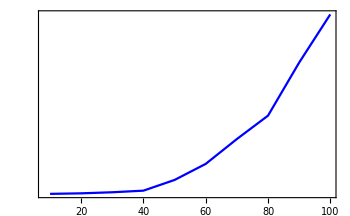
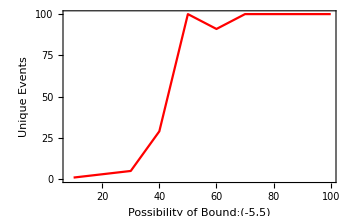

```mathematica
tickvalues={{0,0},{200,200},{400,400},{600,600},{800,800},{1000,1000}};
ticks=MapAt[Rotate[#,Pi/2]&,tickvalues,{All,-1}];
plot3=Overlay[{ListLinePlot[Thread[{xaxis,uniquefluxexchanges}],Frame->True,ImagePadding->35,FrameTicks->{{None,ticks},{All,None}},FrameLabel->{{None,Style["Unique Flux Exchanges",Blue]},{None,None}},PlotStyle->Blue,ImageSize->350,PlotRange->All,ImagePadding->20],ListLinePlot[Thread[{xaxis,uniqueevents}],Frame->True,ImagePadding->35,FrameTicks->{{All,None},{All,None}},FrameLabel->{"Possibility of Bound:(-5,5)",Style["Unique Events",Red]},PlotStyle->Red,ImageSize->350,PlotRange->All,ImagePadding->20]},ImageSize->Large]
```

Model Cartoon

Other Trials

```mathematica
SeedRandom@5;
boundaries=Table[RandomChoice[i->{{0,500},{0,0}},fluxexchanges],{i,Drop[MapThread[{#1,#2}&,{Reverse@Range[0,1,0.1],Range[0,1,0.1]}],-1]}];
```

```mathematica
Drop[MapThread[{#1,#2}&,{Reverse@Range[0,1,0.1],Range[0,1,0.1]}],-1]
Dimensions@boundaries
```

{{1.,0.},{0.9,0.1},{0.8,0.2},{0.7,0.3},{0.6,0.4},{0.5,0.5},{0.4,0.6},{0.3,0.7},{0.2,0.8},{0.1,0.9}}

{10,1008,2}

```mathematica
SeedRandom@5;
AbsoluteTiming[sequencesfixedsubsetsize=Table[Table[syntheticseqgeneratorfxdsubsetsize[stoichiometricmatrix,steadystatevector,i,fluxexchanges,300,500],10],{i,boundaries}];]
sequenceschopped=Table[Chop[i,10^-5],{i,sequencesfixedsubsetsize}];
Table[Length@first[(Flatten[i,1])ᵀ],{i,sequenceschopped}]
Table[Length@(Flatten[i,1])[[first@Flatten[i,1],All]],{i,sequenceschopped}]
```

{774.792,Null}

{3,1,3,3,1,2,1,3,1,1}

{1803,1,1617,1748,1,1638,1,1642,1,1}

```mathematica
SeedRandom@5;
AbsoluteTiming[sequencesfixedsubsetsize=Table[Table[syntheticseqgeneratorfxdsubsetsize[stoichiometricmatrix,steadystatevector,i,fluxexchanges,300,200],10],{i,boundaries}];]
sequenceschopped=Table[Chop[i,10^-5],{i,sequencesfixedsubsetsize}];
Table[Length@first[(Flatten[i,1])ᵀ],{i,sequenceschopped}]
Table[Length@(Flatten[i,1])[[first@Flatten[i,1],All]],{i,sequenceschopped}]
```

{711.616,Null}

{3,1,3,3,1,3,1,3,1,1}

{2410,1,2521,2527,1,2370,1,1932,1,1}

```mathematica
SeedRandom@5;
AbsoluteTiming[sequencesfixedsubsetsize=Table[Table[syntheticseqgeneratorfxdsubsetsize[stoichiometricmatrix,steadystatevector,i,fluxexchanges,300,20],10],{i,boundaries}];]
sequenceschopped=Table[Chop[i,10^-5],{i,sequencesfixedsubsetsize}];
Table[Length@first[(Flatten[i,1])ᵀ],{i,sequenceschopped}]
Table[Length@(Flatten[i,1])[[first@Flatten[i,1],All]],{i,sequenceschopped}]
```

{686.88,Null}

{3,1,3,3,1,3,1,2,1,1}

{3000,1,3000,3000,1,2404,1,7,1,1}

```mathematica
SeedRandom@5;
boundaries=Table[RandomChoice[i->{{0,5},{0,0}},fluxexchanges],{i,Drop[MapThread[{#1,#2}&,{Reverse@Range[0,1,0.1],Range[0,1,0.1]}],-1]}];
```

```mathematica
SeedRandom@5;
AbsoluteTiming[sequencesfixedsubsetsize=Table[Table[syntheticseqgeneratorfxdsubsetsize[stoichiometricmatrix,steadystatevector,i,fluxexchanges,300,20],10],{i,boundaries}];]
sequenceschopped=Table[Chop[i,10^-5],{i,sequencesfixedsubsetsize}];
Table[Length@first[(Flatten[i,1])ᵀ],{i,sequenceschopped}]
Table[Length@(Flatten[i,1])[[first@Flatten[i,1],All]],{i,sequenceschopped}]
```

{943.356,Null}

{3,1,3,3,1,3,1,2,1,1}

{246,1,2143,214,1,256,1,7,1,1}

```mathematica
boundaries=Table[RandomChoice[i->{{-Infinity,Infinity},{0,0}},fluxexchanges],{i,Drop[MapThread[{#1,#2}&,{Reverse@Range[0,1,0.1],Range[0,1,0.1]}],-1]}]
```

```mathematica
SeedRandom@56;
AbsoluteTiming[sequencesfixedsubsetsize=Quiet@Table[Table[syntheticseqgeneratorfxdsubsetsize[stoichiometricmatrix,steadystatevector,i,fluxexchanges,300,20],10],{i,boundaries}];]
sequenceschopped=Table[Chop[i,10^-5],{i,sequencesfixedsubsetsize}];
Table[Length@first[(Flatten[i,1])ᵀ],{i,sequenceschopped}]
Table[Length@(Flatten[i,1])[[first@Flatten[i,1],All]],{i,sequenceschopped}]
```

{3090.45,Null}

```mathematica
SeedRandom@5;
boundaries=Table[{0,i},{i,RandomInteger[{1,10},fluxexchanges]}];
boundaries=Table[ReplacePart[boundaries,Partition[RandomSample[Range@fluxexchanges,Ceiling[0.1*fluxexchanges,1]],1]->{0,0}],{i,Range[0.1,1,0.1]}];
SeedRandom@5;
AbsoluteTiming[sequencesfixedsubsetsize=Table[Table[syntheticseqgeneratorfxdsubsetsize[stoichiometricmatrix,steadystatevector,i,fluxexchanges,300,20],2],{i,boundaries}];]
sequenceschopped=Table[Chop[i,10^-5],{i,sequencesfixedsubsetsize}];
Table[Length@first[(Flatten[i,1])ᵀ],{i,sequenceschopped}]
Table[Length@(Flatten[i,1])[[first@Flatten[i,1],All]],{i,sequenceschopped}]
```

{202.306,Null}

{1,3,3,3,3,3,3,1,3,3}

{1,600,600,600,600,600,600,1,600,600}

```mathematica
syntheticseqgenerator2[stoichiometricmatrix_,steadystatevector_,boundaries_,fluxexchanges_,sequencesize_]:=Module[{subsetsizechoice,subsetpositions,coefficients,objectivefunctions,solutionvectors},
subsetsizechoice=RandomInteger[{1,fluxexchanges}];
subsetpositions=RandomSample[Range@fluxexchanges,subsetsizechoice];
coefficients=Table[RandomReal[{0.1,10},subsetsizechoice],sequencesize];
objectivefunctions=Table[ReplacePart[ConstantArray[0.,fluxexchanges],MapThread[#1->#2&,{subsetpositions,coefficients[[i]]}]],{i,sequencesize}];
solutionvectors=Table[LinearProgramming[-objectivefunctions[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@objectivefunctions}]]
```

```mathematica
SeedRandom@5;
boundaries=Table[{0,i},{i,RandomInteger[{1,10},fluxexchanges]}];
boundaries=Table[ReplacePart[boundaries,Partition[RandomSample[Range@fluxexchanges,Ceiling[0.1*fluxexchanges,1]],1]->{0,0}],{i,Range[0.1,1,0.1]}];
```

```mathematica
AbsoluteTiming[sequencesfixedsubsetsize=Table[Table[syntheticseqgenerator2[stoichiometricmatrix,steadystatevector,i,fluxexchanges,300],2],{i,boundaries}];]
sequenceschopped=Table[Chop[i,10^-5],{i,sequencesfixedsubsetsize}];
Table[Length@first[(Flatten[i,1])ᵀ],{i,sequenceschopped}]
Table[Length@(Flatten[i,1])[[first@Flatten[i,1],All]],{i,sequenceschopped}]
```

{195.126,Null}

{1,3,3,3,3,3,3,1,3,3}

{1,595,505,590,600,598,596,1,598,600}

Trials with different boundary limits

```mathematica
sequencesize=300;
boundaries=Table[{0,i},{i,RandomInteger[{-200,200},fluxexchanges]}];
```

```mathematica
subsetsizechoice=250;
subsetpositions=RandomSample[Range@fluxexchanges,subsetsizechoice];
coefficients=Table[RandomReal[{-2,2},subsetsizechoice],sequencesize];
objectivefunctions=Table[ReplacePart[ConstantArray[0.,fluxexchanges],MapThread[#1->#2&,{subsetpositions,coefficients[[i]]}]],{i,sequencesize}];
solutionvectors=Table[LinearProgramming[-objectivefunctions[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@objectivefunctions}];
sequenceschopped=Chop[solutionvectors,10^-5];
Length@first[(Flatten[sequenceschopped,1])ᵀ]
Length@(Flatten[sequenceschopped,1])[[first@Flatten[sequenceschopped,1],All]]
```

300

```mathematica
boundaries=ConstantArray[{-500,500},fluxexchanges];
SeedRandom@5;
AbsoluteTiming[sequencesfixedsubsetsize=Table[Table[syntheticseqgeneratorfxdsubsetsizevaryingcoeff[stoichiometricmatrix,steadystatevector,boundaries,fluxexchanges,10,20,i],10],{i,coefboundaries}];]
sequenceschopped=Table[Chop[i,10^-5],{i,sequencesfixedsubsetsize}];
Table[Length@first[(Flatten[i,1])ᵀ],{i,sequenceschopped}]
Table[Length@(Flatten[i,1])[[first@Flatten[i,1],All]],{i,sequenceschopped}]
```

{31.4049,Null}

{1006,1007,1004,1005,1004,1005,1005,1006,1006,1003}

{100,100,100,100,100,100,100,100,100,10}